n1 (Original) = Cos[ⅇ^((x+y)/2)]+ⅈ Sin[ⅇ^((x+y)/2)]

n2_cand (Ghost Branch) = (ⅇ^(1/2 (2 ⅈ √(ⅇ^(x+y))+x+y)) (-ⅈ+ⅇ^((x+y)/2)))/(ⅇ^(x+y)+ⅈ √(ⅇ^(x+y)))

Curvature Error (w2 - w1) = -((1/2+ⅈ/2) ⅇ^(ⅈ √(ⅇ^(x+y))) (2 √(ⅇ^(x+y))+ⅇ^((x+y)/2) (2-3 ⅇ^(x+y)-ⅇ^(2 (x+y))+ⅈ √(ⅇ^(x+y)) (5+ⅇ^(x+y))+ⅇ^((3 (x+y))/2) (ⅈ+√(ⅇ^(x+y)))+ⅇ^((x+y)/2) (ⅈ+3 √(ⅇ^(x+y))))))/((1+ⅇ^(x+y))^2)

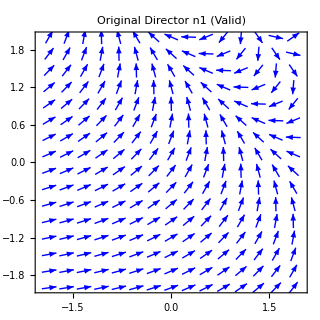
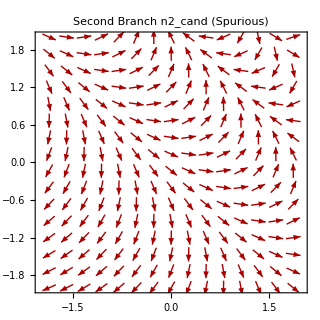

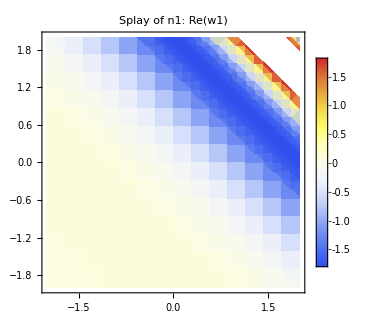
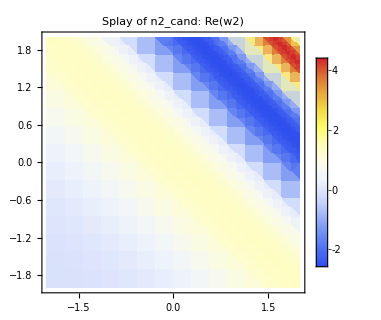

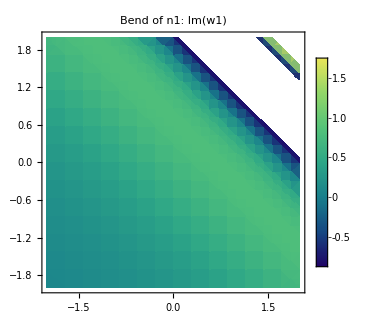
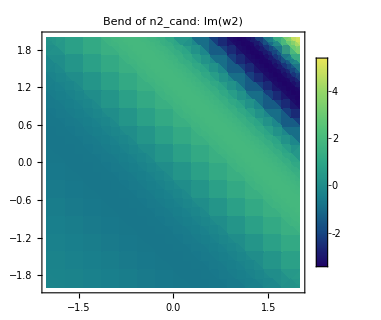

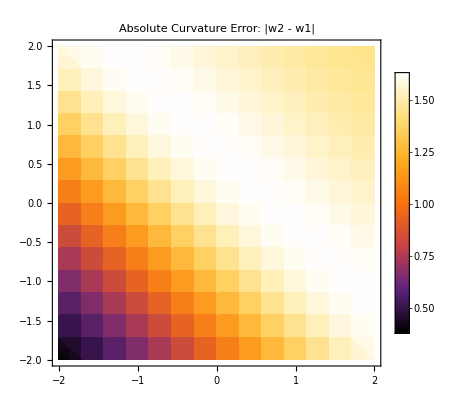

Files successfully saved at:
C:\Users\yarde\OneDrive - weizmann.ac.il\שולחן העבודה\WSOS\Efi efrati\קוד\cheack n's\E^((x+y)\2)

n1 (Original) = Cos[x+y^2/2]+ⅈ Sin[x+y^2/2]

n2_cand (Ghost Branch) = (ⅇ^(1/2 ⅈ (2 x+y^2)) ((1-ⅈ)+y^2))/((1+ⅈ)+y^2)

Curvature Error (w2 - w1) = (2 ⅇ^(1/2 ⅈ (2 x+y^2)) ((1+ⅈ)+y ((3-ⅈ)+y-ⅈ y^2)))/(((1+ⅈ)+y^2)^2)

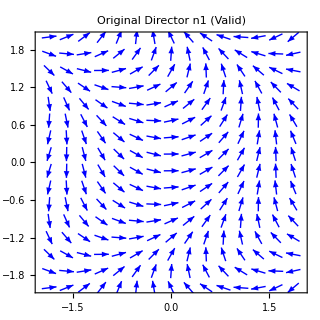
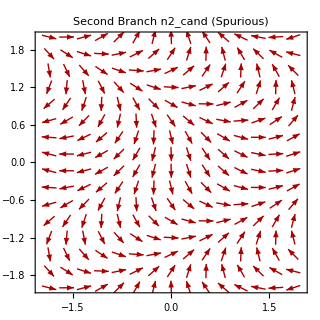

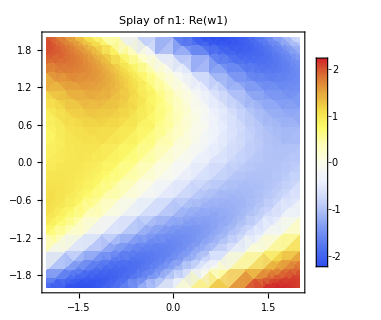
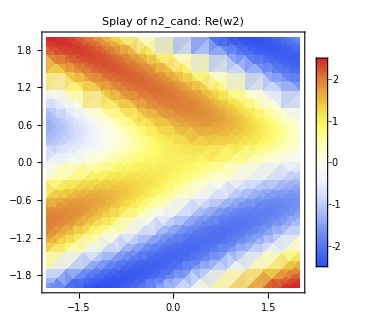

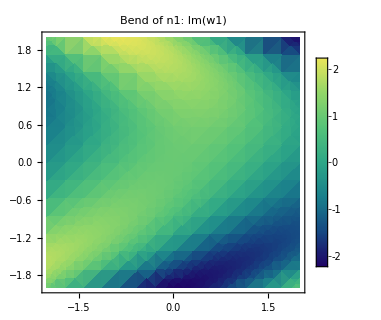
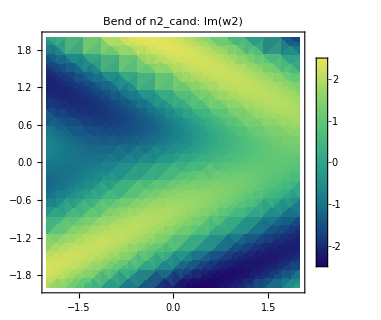

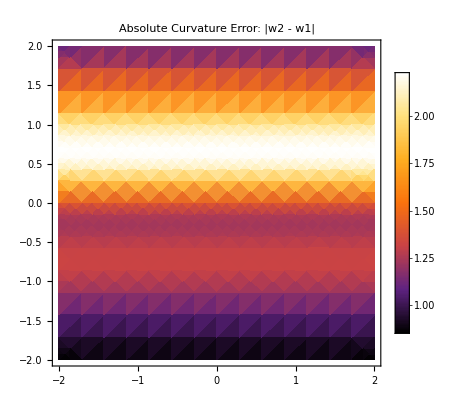

Files successfully saved at:
C:\Users\yarde\OneDrive - weizmann.ac.il\שולחן העבודה\WSOS\Efi efrati\קוד\cheack n's\SmoothField_Theta_x_y2

```mathematica
ClearAll["Global`*"];

twoDz[f_]:=D[f,x]-I*D[f,y];
twoDzbar[f_]:=D[f,x]+I*D[f,y];
conj[expr_]:=ComplexExpand[Conjugate[expr],TargetFunctions->{Re,Im}];
absSq[expr_]:=Expand[expr*conj[expr]];

(* ==========================================*)
(*הגדרת שם הדוגמה ויצירת התיקייה הייעודית*)
(* ==========================================*)
exampleName="E^((x+y)/2)";
targetDir=FileNameJoin[{NotebookDirectory[],exampleName}];

If[!DirectoryQ[targetDir],CreateDirectory[targetDir]];

(*1. הגדרת השדה החלק n1 ללא שום פגם טופולוגי*)
theta1[x_,y_]:=Exp[(x+y)/2];
n1=Cos[theta1[x,y]]+I*Sin[theta1[x,y]];
w1=FullSimplify[ComplexExpand[twoDz[n1]]];

(*2. חילוץ הענף האלגברי השני n2_cand מתוך נוסחת השחזור*)
w1AbsSq=FullSimplify[absSq[w1]];
w1Dzbar=FullSimplify[ComplexExpand[twoDzbar[w1]]];
w1DzbarBar=FullSimplify[conj[w1Dzbar]];
Rexpr=FullSimplify[Sqrt[absSq[w1Dzbar]-w1AbsSq^2],Assumptions->{x∈Reals,y∈Reals}];

(*הענף השלילי (-I*R) מחזיר את n1,והענף החיובי (+I*R) נותן את המועמד השני n2Cand*)
n2Cand=FullSimplify[(-w1AbsSq+I*Rexpr)/w1DzbarBar];
w2Cand=FullSimplify[ComplexExpand[twoDz[n2Cand]]];

errorExpr=FullSimplify[w2Cand-w1];

Print[Style["n1 (Original) = ",Bold,Blue],n1];
Print[Style["n2_cand (Ghost Branch) = ",Bold,Red],n2Cand];
Print[Style["Curvature Error (w2 - w1) = ",Bold,Purple],errorExpr];

(*3. שרטוט שני שדות הדירקטור (שניהם באורך 1 וללא פגמים!)*)
plotN1=VectorPlot[{Re[n1],Im[n1]},{x,-2,2},{y,-2,2},PlotLabel->Style["Original Director n1 (Valid)",Bold,Blue],VectorStyle->Blue,VectorColorFunction->None,VectorScale->{Tiny,Automatic,None},ImageSize->320];

plotN2=VectorPlot[Evaluate[ComplexExpand[{Re[n2Cand],Im[n2Cand]}]],{x,-2,2},{y,-2,2},PlotLabel->Style["Second Branch n2_cand (Spurious)",Bold,Darker[Red]],VectorStyle->Darker[Red],VectorColorFunction->None,VectorScale->{Tiny,Automatic,None},ImageSize->320];

Print[Row[{plotN1,plotN2},Spacer[20]]];

(*4. השוואת Splay (החלק הממשי) של n1 מול n2_cand*)
plotS1=DensityPlot[Evaluate[ComplexExpand[Re[w1]]],{x,-2,2},{y,-2,2},PlotLabel->"Splay of n1: Re(w1)",ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->320];

plotS2=DensityPlot[Evaluate[ComplexExpand[Re[w2Cand]]],{x,-2,2},{y,-2,2},PlotLabel->"Splay of n2_cand: Re(w2)",ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->320];

Print[Row[{plotS1,plotS2},Spacer[20]]];

(*5. השוואת Bend (החלק המדומה) של n1 מול n2_cand*)
plotB1=DensityPlot[Evaluate[ComplexExpand[Im[w1]]],{x,-2,2},{y,-2,2},PlotLabel->"Bend of n1: Im(w1)",ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,ImageSize->320];

plotB2=DensityPlot[Evaluate[ComplexExpand[Im[w2Cand]]],{x,-2,2},{y,-2,2},PlotLabel->"Bend of n2_cand: Im(w2)",ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,ImageSize->320];

Print[Row[{plotB1,plotB2},Spacer[20]]];

(*6. ויזואליזציה של שגיאת העקמומיות הכוללת (ההפרש המוחלט)*)
plotError=DensityPlot[Evaluate[Abs[errorExpr]],{x,-2,2},{y,-2,2},PlotLabel->Style["Absolute Curvature Error: |w2 - w1|",Bold,Purple],ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->400];

Print[plotError];

(* ==========================================*)
(*ייצוא ושמירת הקבצים בתיקייה החדשה*)
(* ==========================================*)

(*יצירת מסמך טקסט עם נתוני הריצה*)
dataDocument="Simulation Data - "<>exampleName<>"\n"<>"========================================\n\n"<>"Theta1: \n"<>ToString[StandardForm[theta1[x,y]]]<>"\n\n"<>"Original Director (n1): \n"<>ToString[StandardForm[n1]]<>"\n\n"<>"Ghost Branch Director (n2_cand): \n"<>ToString[StandardForm[n2Cand]]<>"\n\n"<>"Curvature Error (w2 - w1): \n"<>ToString[StandardForm[errorExpr]]<>"\n";

Export[FileNameJoin[{targetDir,"0_Simulation_Data.txt"}],dataDocument];

(*שמירת התמונות עם שמות קריאים ומסודרים*)
Export[FileNameJoin[{targetDir,"1_Comparison_Directors.png"}],Row[{plotN1,plotN2},Spacer[20]]];
Export[FileNameJoin[{targetDir,"2_Comparison_Splay.png"}],Row[{plotS1,plotS2},Spacer[20]]];
Export[FileNameJoin[{targetDir,"3_Comparison_Bend.png"}],Row[{plotB1,plotB2},Spacer[20]]];

Export[FileNameJoin[{targetDir,"4_Original_Director_n1.png"}],plotN1,ImageResolution->300];
Export[FileNameJoin[{targetDir,"5_Spurious_Director_n2.png"}],plotN2,ImageResolution->300];
Export[FileNameJoin[{targetDir,"6_Splay_Map_n1.png"}],plotS1,ImageResolution->300];
Export[FileNameJoin[{targetDir,"7_Splay_Map_n2.png"}],plotS2,ImageResolution->300];
Export[FileNameJoin[{targetDir,"8_Bend_Map_n1.png"}],plotB1,ImageResolution->300];
Export[FileNameJoin[{targetDir,"9_Bend_Map_n2.png"}],plotB2,ImageResolution->300];
Export[FileNameJoin[{targetDir,"10_Curvature_Error_Map.png"}],plotError,ImageResolution->300];

(*הצגת נתיב השמירה במסך*)
Print[Style["Files successfully saved at:\n",Bold,Darker[Green]],targetDir];ClearAll["Global`*"];

twoDz[f_]:=D[f,x]-I*D[f,y];
twoDzbar[f_]:=D[f,x]+I*D[f,y];
conj[expr_]:=ComplexExpand[Conjugate[expr],TargetFunctions->{Re,Im}];
absSq[expr_]:=Expand[expr*conj[expr]];

(* ==========================================*)
(*הגדרת שם הדוגמה ויצירת התיקייה הייעודית*)
(* ==========================================*)
exampleName="SmoothField_Theta_x_y2";
targetDir=FileNameJoin[{NotebookDirectory[],exampleName}];

If[!DirectoryQ[targetDir],CreateDirectory[targetDir]];

(*1. הגדרת השדה החלק n1 ללא שום פגם טופולוגי*)
theta1[x_,y_]:=x+y^2/2;
n1=Cos[theta1[x,y]]+I*Sin[theta1[x,y]];
w1=FullSimplify[ComplexExpand[twoDz[n1]]];

(*2. חילוץ הענף האלגברי השני n2_cand מתוך נוסחת השחזור*)
w1AbsSq=FullSimplify[absSq[w1]];
w1Dzbar=FullSimplify[ComplexExpand[twoDzbar[w1]]];
w1DzbarBar=FullSimplify[conj[w1Dzbar]];
Rexpr=FullSimplify[Sqrt[absSq[w1Dzbar]-w1AbsSq^2],Assumptions->{x∈Reals,y∈Reals}];

(*הענף השלילי (-I*R) מחזיר את n1,והענף החיובי (+I*R) נותן את המועמד השני n2Cand*)
n2Cand=FullSimplify[(-w1AbsSq+I*Rexpr)/w1DzbarBar];
w2Cand=FullSimplify[ComplexExpand[twoDz[n2Cand]]];

errorExpr=FullSimplify[w2Cand-w1];

Print[Style["n1 (Original) = ",Bold,Blue],n1];
Print[Style["n2_cand (Ghost Branch) = ",Bold,Red],n2Cand];
Print[Style["Curvature Error (w2 - w1) = ",Bold,Purple],errorExpr];

(*3. שרטוט שני שדות הדירקטור (שניהם באורך 1 וללא פגמים!)*)
plotN1=VectorPlot[{Re[n1],Im[n1]},{x,-2,2},{y,-2,2},PlotLabel->Style["Original Director n1 (Valid)",Bold,Blue],VectorStyle->Blue,VectorColorFunction->None,VectorScale->{Tiny,Automatic,None},ImageSize->320];

plotN2=VectorPlot[Evaluate[ComplexExpand[{Re[n2Cand],Im[n2Cand]}]],{x,-2,2},{y,-2,2},PlotLabel->Style["Second Branch n2_cand (Spurious)",Bold,Darker[Red]],VectorStyle->Darker[Red],VectorColorFunction->None,VectorScale->{Tiny,Automatic,None},ImageSize->320];

Print[Row[{plotN1,plotN2},Spacer[20]]];

(*4. השוואת Splay (החלק הממשי) של n1 מול n2_cand*)
plotS1=DensityPlot[Evaluate[ComplexExpand[Re[w1]]],{x,-2,2},{y,-2,2},PlotLabel->"Splay of n1: Re(w1)",ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->320];

plotS2=DensityPlot[Evaluate[ComplexExpand[Re[w2Cand]]],{x,-2,2},{y,-2,2},PlotLabel->"Splay of n2_cand: Re(w2)",ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->320];

Print[Row[{plotS1,plotS2},Spacer[20]]];

(*5. השוואת Bend (החלק המדומה) של n1 מול n2_cand*)
plotB1=DensityPlot[Evaluate[ComplexExpand[Im[w1]]],{x,-2,2},{y,-2,2},PlotLabel->"Bend of n1: Im(w1)",ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,ImageSize->320];

plotB2=DensityPlot[Evaluate[ComplexExpand[Im[w2Cand]]],{x,-2,2},{y,-2,2},PlotLabel->"Bend of n2_cand: Im(w2)",ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,ImageSize->320];

Print[Row[{plotB1,plotB2},Spacer[20]]];

(*6. ויזואליזציה של שגיאת העקמומיות הכוללת (ההפרש המוחלט)*)
plotError=DensityPlot[Evaluate[Abs[errorExpr]],{x,-2,2},{y,-2,2},PlotLabel->Style["Absolute Curvature Error: |w2 - w1|",Bold,Purple],ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->400];

Print[plotError];

(* ==========================================*)
(*ייצוא ושמירת הקבצים בתיקייה החדשה*)
(* ==========================================*)

(*יצירת מסמך טקסט עם נתוני הריצה*)
dataDocument="Simulation Data - "<>exampleName<>"\n"<>"========================================\n\n"<>"Theta1: \n"<>ToString[StandardForm[theta1[x,y]]]<>"\n\n"<>"Original Director (n1): \n"<>ToString[StandardForm[n1]]<>"\n\n"<>"Ghost Branch Director (n2_cand): \n"<>ToString[StandardForm[n2Cand]]<>"\n\n"<>"Curvature Error (w2 - w1): \n"<>ToString[StandardForm[errorExpr]]<>"\n";

Export[FileNameJoin[{targetDir,"0_Simulation_Data.txt"}],dataDocument];

(*שמירת התמונות עם שמות קריאים ומסודרים*)
Export[FileNameJoin[{targetDir,"1_Comparison_Directors.png"}],Row[{plotN1,plotN2},Spacer[20]]];
Export[FileNameJoin[{targetDir,"2_Comparison_Splay.png"}],Row[{plotS1,plotS2},Spacer[20]]];
Export[FileNameJoin[{targetDir,"3_Comparison_Bend.png"}],Row[{plotB1,plotB2},Spacer[20]]];

Export[FileNameJoin[{targetDir,"4_Original_Director_n1.png"}],plotN1,ImageResolution->300];
Export[FileNameJoin[{targetDir,"5_Spurious_Director_n2.png"}],plotN2,ImageResolution->300];
Export[FileNameJoin[{targetDir,"6_Splay_Map_n1.png"}],plotS1,ImageResolution->300];
Export[FileNameJoin[{targetDir,"7_Splay_Map_n2.png"}],plotS2,ImageResolution->300];
Export[FileNameJoin[{targetDir,"8_Bend_Map_n1.png"}],plotB1,ImageResolution->300];
Export[FileNameJoin[{targetDir,"9_Bend_Map_n2.png"}],plotB2,ImageResolution->300];
Export[FileNameJoin[{targetDir,"10_Curvature_Error_Map.png"}],plotError,ImageResolution->300];

(*הצגת נתיב השמירה במסך*)
Print[Style["Files successfully saved at:\n",Bold,Darker[Green]],targetDir];
```